```mathematica
a1=Table[{a,b,a+b},{a,0,9},{b,0,9}];
```

```mathematica
a2=Table[{a,b,a*b},{a,0,9},{b,0,9}];
```

```mathematica
a3=Table[{a,b,a-b},{a,0,9},{b,0,9}];
```

```mathematica
a4=Table[{a,b,a/b},{a,0,9},{b,1,9}];
```

```mathematica
a5=Select[Flatten[a1,1],#[[3]]>9&];
```

```mathematica
a6=Select[Flatten[a2,1],#[[3]]>9&];
```

```mathematica
b1=Map[{#[[1]],#[[2]],Floor[#[[3]]/10],Mod[#[[3]],10]}&,a5~Join~a6];
```

```mathematica
b2=Map[RotateLeft,b1];
```

```mathematica
b3=Map[RotateLeft,b2];
```

```mathematica
a=Select[Flatten[Join[a1,a2,a3,a4],1],IntegerQ[#[[3]]]&&#[[3]]≥0&&#[[1]]=!=#[[2]]&]
```

{{0,1,1},{0,2,2},{0,3,3},{0,4,4},{0,5,5},{0,6,6},{0,7,7},{0,8,8},{0,9,9},{1,0,1},{1,2,3},{1,3,4},{1,4,5},{1,5,6},{1,6,7},{1,7,8},{1,8,9},{1,9,10},{2,0,2},{2,1,3},{2,3,5},{2,4,6},{2,5,7},{2,6,8},{2,7,9},{2,8,10},{2,9,11},{3,0,3},{3,1,4},{3,2,5},{3,4,7},{3,5,8},{3,6,9},{3,7,10},{3,8,11},{3,9,12},{4,0,4},{4,1,5},{4,2,6},{4,3,7},{4,5,9},{4,6,10},{4,7,11},{4,8,12},{4,9,13},{5,0,5},{5,1,6},{5,2,7},{5,3,8},{5,4,9},{5,6,11},{5,7,12},{5,8,13},{5,9,14},{6,0,6},{6,1,7},{6,2,8},{6,3,9},{6,4,10},{6,5,11},{6,7,13},{6,8,14},{6,9,15},{7,0,7},{7,1,8},{7,2,9},{7,3,10},{7,4,11},{7,5,12},{7,6,13},{7,8,15},{7,9,16},{8,0,8},{8,1,9},{8,2,10},{8,3,11},{8,4,12},{8,5,13},{8,6,14},{8,7,15},{8,9,17},{9,0,9},{9,1,10},{9,2,11},{9,3,12},{9,4,13},{9,5,14},{9,6,15},{9,7,16},{9,8,17},{0,1,0},{0,2,0},{0,3,0},{0,4,0},{0,5,0},{0,6,0},{0,7,0},{0,8,0},{0,9,0},{1,0,0},{1,2,2},{1,3,3},{1,4,4},{1,5,5},{1,6,6},{1,7,7},{1,8,8},{1,9,9},{2,0,0},{2,1,2},{2,3,6},{2,4,8},{2,5,10},{2,6,12},{2,7,14},{2,8,16},{2,9,18},{3,0,0},{3,1,3},{3,2,6},{3,4,12},{3,5,15},{3,6,18},{3,7,21},{3,8,24},{3,9,27},{4,0,0},{4,1,4},{4,2,8},{4,3,12},{4,5,20},{4,6,24},{4,7,28},{4,8,32},{4,9,36},{5,0,0},{5,1,5},{5,2,10},{5,3,15},{5,4,20},{5,6,30},{5,7,35},{5,8,40},{5,9,45},{6,0,0},{6,1,6},{6,2,12},{6,3,18},{6,4,24},{6,5,30},{6,7,42},{6,8,48},{6,9,54},{7,0,0},{7,1,7},{7,2,14},{7,3,21},{7,4,28},{7,5,35},{7,6,42},{7,8,56},{7,9,63},{8,0,0},{8,1,8},{8,2,16},{8,3,24},{8,4,32},{8,5,40},{8,6,48},{8,7,56},{8,9,72},{9,0,0},{9,1,9},{9,2,18},{9,3,27},{9,4,36},{9,5,45},{9,6,54},{9,7,63},{9,8,72},{1,0,1},{2,0,2},{2,1,1},{3,0,3},{3,1,2},{3,2,1},{4,0,4},{4,1,3},{4,2,2},{4,3,1},{5,0,5},{5,1,4},{5,2,3},{5,3,2},{5,4,1},{6,0,6},{6,1,5},{6,2,4},{6,3,3},{6,4,2},{6,5,1},{7,0,7},{7,1,6},{7,2,5},{7,3,4},{7,4,3},{7,5,2},{7,6,1},{8,0,8},{8,1,7},{8,2,6},{8,3,5},{8,4,4},{8,5,3},{8,6,2},{8,7,1},{9,0,9},{9,1,8},{9,2,7},{9,3,6},{9,4,5},{9,5,4},{9,6,3},{9,7,2},{9,8,1},{0,1,0},{0,2,0},{0,3,0},{0,4,0},{0,5,0},{0,6,0},{0,7,0},{0,8,0},{0,9,0},{2,1,2},{3,1,3},{4,1,4},{4,2,2},{5,1,5},{6,1,6},{6,2,3},{6,3,2},{7,1,7},{8,1,8},{8,2,4},{8,4,2},{9,1,9},{9,3,3}}

```mathematica
b={};
For[i=1,i≤Length[a],i++,
For[j=1,j≤Length[a],j++,
If[a[[i,3]]==a[[j,3]],AppendTo[b,{a[[i,1]],a[[i,2]],a[[j,1]],a[[j,2]]}];AppendTo[b,{a[[j,1]],a[[j,2]],a[[i,1]],a[[i,2]]}]]]]
```

```mathematica
b=Select[b,Length[Union[#]]==4&];
```

```mathematica
Length[b]
```

2796

```mathematica
filter[L_]:=Select[b,MemberQ[L,#[[2]]]&&MemberQ[L,#[[3]]]&&Not[MemberQ[L,#[[1]]]]&&Not[MemberQ[L,#[[4]]]]&]
```

```mathematica
S={};
For[i1=1,i1≤Length[b],i1++,If[Mod[i1,100]==0,Print[i1]];
b1=b[[i1]];
For[i2=1,i2≤Length[b],i2++,
b2=b[[i2]];
If[Length[Union[Flatten[{b1,b2}]]]==7&&b1[[1]]==b2[[1]],
For[i3=1,i3≤Length[b],i3++,
b3=b[[i3]];
If[Length[Union[Flatten[{b1,b2,b3}]]]==9&&b1[[2]]==b3[[3]]&&b2[[2]]==b3[[2]],
missing=Complement[Range[0,9],Union[Flatten[{b1,b2,b3}]]][[1]];
If[MemberQ[b,{b3[[1]],b2[[3]],missing,b1[[4]]}]&&MemberQ[b,{b3[[4]],b1[[3]],missing,b2[[4]]}],AppendTo[S,{b1,b2,b3,{b3[[1]],b2[[3]],missing,b1[[4]]},{b3[[4]],b1[[3]],missing,b2[[4]]}}]]]]]]]
```

100

200

300

400

500

600

700

800

900

1000

1100

1200

1300

1400

1500

1600

1700

1800

1900

2000

2100

2200

2300

2400

2500

2600

2700

```mathematica
S=Union[S];
```

```mathematica
Length[S]
```

846

```mathematica
sign[Plus]=Style["+",FontSize->30];
sign[Times]=Style["×",FontSize->30];
sign[Subtract]=Style["-",FontSize->30];
sign[Divide]=Style["÷",FontSize->30];
```

```mathematica
q[r_,t_]:=r{Sin[2Pi t/5],Cos[2Pi t/5]}
```

```mathematica
pic[oper_,L_]:=Module[{},
Print[Show[Graphics[{RGBColor[1.,0.843104,0.],
Table[Disk[q[3,k+1/2],1],{k,1,5}],
Table[Disk[q[5 GoldenRatio ,k],1],{k,1,5}],Black,
Table[Circle[q[3,k+1/2],1],{k,1,5}],
Table[Circle[q[5 GoldenRatio ,k],1],{k,1,5}],
Table[Text[Style["=",FontSize->30],{2.5Sin[2Pi k/5],2.5Cos[2Pi k/5]}],{k,1,5}],
Text[sign[oper[[1]]],(q[3,4.5]+q[5GoldenRatio,4])/2],Text[sign[oper[[2]]],(q[3,.5]+q[5GoldenRatio,1])/2],Text[sign[oper[[3]]],(q[3,3.5]+q[5GoldenRatio,4])/2],Text[sign[oper[[4]]],(q[3,2.5]+q[5GoldenRatio,2])/2],Text[sign[oper[[5]]],(q[3,3.5]+q[5GoldenRatio,3])/2],Text[sign[oper[[6]]],(q[3,4.5]+q[5GoldenRatio,5])/2],Text[sign[oper[[7]]],(q[3,2.5]+q[5GoldenRatio,3])/2],Text[sign[oper[[8]]],(q[3,1.5]+q[5GoldenRatio,1])/2],Text[sign[oper[[9]]],(q[3,.5]+q[5GoldenRatio,0])/2],Text[sign[oper[[10]]],(q[3,1.5]+q[5GoldenRatio,2])/2]
}],ImageSize->300]];
Print[Show[Graphics[{RGBColor[1.,0.843104,0.],
Table[Disk[q[3,k+1/2],1],{k,1,5}],
Table[Disk[q[5 GoldenRatio ,k],1],{k,1,5}],Black,
Table[Circle[q[3,k+1/2],1],{k,1,5}],
Table[Circle[q[5 GoldenRatio ,k],1],{k,1,5}],
Table[Text[Style["=",FontSize->30],{2.5Sin[2Pi k/5],2.5Cos[2Pi k/5]}],{k,1,5}],
Text[sign[oper[[1]]],(q[3,4.5]+q[5GoldenRatio,4])/2],Text[sign[oper[[2]]],(q[3,.5]+q[5GoldenRatio,1])/2],Text[sign[oper[[3]]],(q[3,3.5]+q[5GoldenRatio,4])/2],Text[sign[oper[[4]]],(q[3,2.5]+q[5GoldenRatio,2])/2],Text[sign[oper[[5]]],(q[3,3.5]+q[5GoldenRatio,3])/2],Text[sign[oper[[6]]],(q[3,4.5]+q[5GoldenRatio,5])/2],Text[sign[oper[[7]]],(q[3,2.5]+q[5GoldenRatio,3])/2],Text[sign[oper[[8]]],(q[3,1.5]+q[5GoldenRatio,1])/2],Text[sign[oper[[9]]],(q[3,.5]+q[5GoldenRatio,0])/2],Text[sign[oper[[10]]],(q[3,1.5]+q[5GoldenRatio,2])/2],
Text[Style[L[[1,1,1]],FontSize->24],q[5GoldenRatio,4]],
Text[Style[L[[1,1,2]],FontSize->24],q[3,4.5]],
Text[Style[L[[1,1,3]],FontSize->24],q[3,.5]],
Text[Style[L[[1,1,4]],FontSize->24],q[5GoldenRatio,1]],
Text[Style[L[[1,2,2]],FontSize->24],q[3,3.5]],
Text[Style[L[[1,2,3]],FontSize->24],q[3,2.5]],
Text[Style[L[[1,2,4]],FontSize->24],q[5GoldenRatio,2]],
Text[Style[L[[1,3,1]],FontSize->24],q[5GoldenRatio,3]],
Text[Style[L[[1,3,4]],FontSize->24],q[5GoldenRatio,5]],
Text[Style[L[[1,4,3]],FontSize->24],q[3,1.5]]
}],ImageSize->300]]];
```

```mathematica
ops={Plus,Times,Subtract,Divide};
```

```mathematica
For[j=1,j<10000,j++,
For[i=1,i≤10,i++,p[i]=ops[[RandomInteger[{1,4}]]]];
sel=Select[S,p[1][#[[1,1]],#[[1,2]]]==p[2][#[[1,3]],#[[1,4]]]&&p[3][#[[2,1]],#[[2,2]]]==p[4][#[[2,3]],#[[2,4]]]&&p[5][#[[3,1]],#[[3,2]]]==p[6][#[[3,3]],#[[3,4]]]&&p[7][#[[4,1]],#[[4,2]]]==p[8][#[[4,3]],#[[4,4]]]&&p[9][#[[5,1]],#[[5,2]]]==p[10][#[[5,3]],#[[5,4]]]&];
If[Length[sel]==1,pic[Table[p[i],{i,1,10}],sel]]]
```

Insert the digits 0-9 into the circles to make the 5 equations true when read from left to right. Each digit is used exactly once.

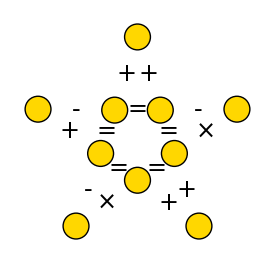

ANSWER